In this scripts it is made the Clustering analysis of the

## Exploring the estimators for clustering

```mathematica
ff[dato_]:=N[Variance[dato]/Mean[dato]]
cv[data_]:=N[StandardDeviation[data]/Mean[data]]
cv2[data_]:=cv[data]^2
```

```mathematica
mRNAMolecules=listDataAndTimeTN[[1,All,2,1]];
proteinMolecules=listDataAndTimeTN[[1,All,2,2]];
```

```mathematica
mRNAMolecules=RandomVariate[NormalDistribution[2,0.4],100000];
proteinMolecules=RandomVariate[NormalDistribution[6,4],1000];
```

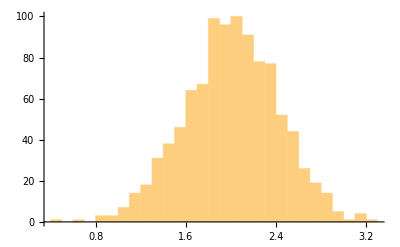
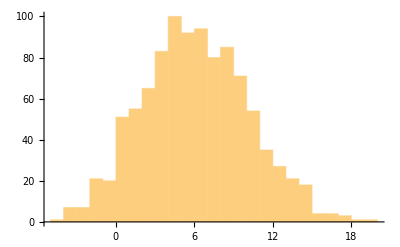

```mathematica
{Histogram[mRNAMolecules],Histogram[proteinMolecules]}
```

```mathematica
Skewness[mRNAMolecules]
```

-0.116417

```mathematica
Kurtosis[mRNAMolecules]
```

3.09893

```mathematica
Mean[#]&@mRNAMolecules
```

2.00465

```mathematica
{Mean[#],Variance[#],StandardDeviation[#],ff[#],cv[#],cv2[#],cv[#]^2,Variance[#]/Mean[#]^2,Kurtosis[#],Skewness[#]}&@mRNAMolecules
```

{2.00122,0.159446,0.399307,0.0796745,0.199532,0.039813,0.039813,0.039813,2.9929,0.00988591}

```mathematica
Table[Moment[mRNAMolecules,i],{i,10}]
```

{2.00122,4.16431,8.97247,19.9514,45.6634,107.334,258.619,637.723,1607.05,4133.33}

```mathematica
Table[CentralMoment[mRNAMolecules,i],{i,10}]
```

{0.,0.159444,0.000629404,0.0760868,0.000734421,0.0601482,0.00080426,0.0659191,0.00107544,0.0916558}

```mathematica
{#,Exp[#]}&/@{0.15,0.074,0.041,0.277,0.864,1.087,1.127,0.120,0.213,0.167,0.727,0.105,-0.522,0.982,0.215,0.392,0.592,1.147,1.270,1.25,0.727,0.105,-0.522,0.982,0.215,0.392}
```

{{0.15,1.16183},{0.074,1.07681},{0.041,1.04185},{0.277,1.31917},{0.864,2.37263},{1.087,2.96536},{1.127,3.08638},{0.12,1.1275},{0.213,1.23738},{0.167,1.18175},{0.727,2.06886},{0.105,1.11071},{-0.522,0.593333},{0.982,2.66979},{0.215,1.23986},{0.392,1.47994},{0.592,1.8076},{1.147,3.14873},{1.27,3.56085},{1.25,3.49034},{0.727,2.06886},{0.105,1.11071},{-0.522,0.593333},{0.982,2.66979},{0.215,1.23986},{0.392,1.47994}}

## Selecting the set of parameters

Here we selected ___ set the parameters for the total range of both kon and koff parameters values. With this set we estimate the statistical significance between regulatory systems and run the clustering algorithm.

```mathematica
kgs=Range[0.01,1,0.01];
γgs=Range[0.02,2,0.02];
```

```mathematica
nDivisiones=10;
```

```mathematica
allCuadrillas=Map[Flatten[#,1]&,Flatten[Table[Outer[List,Partition[kgs,nDivisiones][[i]],Partition[γgs,nDivisiones][[j]]],{i,nDivisiones},{j,nDivisiones}],1]];
```

```mathematica
allCuadrillas//Dimensions
```

{100,100,2}

```mathematica
allCuadrillas[[1]]
```

{{0.01,0.02},{0.01,0.04},{0.01,0.06},{0.01,0.08},{0.01,0.1},{0.01,0.12},{0.01,0.14},{0.01,0.16},{0.01,0.18},{0.01,0.2},{0.02,0.02},{0.02,0.04},{0.02,0.06},{0.02,0.08},{0.02,0.1},{0.02,0.12},{0.02,0.14},{0.02,0.16},{0.02,0.18},{0.02,0.2},{0.03,0.02},{0.03,0.04},{0.03,0.06},{0.03,0.08},{0.03,0.1},{0.03,0.12},{0.03,0.14},{0.03,0.16},{0.03,0.18},{0.03,0.2},{0.04,0.02},{0.04,0.04},{0.04,0.06},{0.04,0.08},{0.04,0.1},{0.04,0.12},{0.04,0.14},{0.04,0.16},{0.04,0.18},{0.04,0.2},{0.05,0.02},{0.05,0.04},{0.05,0.06},{0.05,0.08},{0.05,0.1},{0.05,0.12},{0.05,0.14},{0.05,0.16},{0.05,0.18},{0.05,0.2},{0.06,0.02},{0.06,0.04},{0.06,0.06},{0.06,0.08},{0.06,0.1},{0.06,0.12},{0.06,0.14},{0.06,0.16},{0.06,0.18},{0.06,0.2},{0.07,0.02},{0.07,0.04},{0.07,0.06},{0.07,0.08},{0.07,0.1},{0.07,0.12},{0.07,0.14},{0.07,0.16},{0.07,0.18},{0.07,0.2},{0.08,0.02},{0.08,0.04},{0.08,0.06},{0.08,0.08},{0.08,0.1},{0.08,0.12},{0.08,0.14},{0.08,0.16},{0.08,0.18},{0.08,0.2},{0.09,0.02},{0.09,0.04},{0.09,0.06},{0.09,0.08},{0.09,0.1},{0.09,0.12},{0.09,0.14},{0.09,0.16},{0.09,0.18},{0.09,0.2},{0.1,0.02},{0.1,0.04},{0.1,0.06},{0.1,0.08},{0.1,0.1},{0.1,0.12},{0.1,0.14},{0.1,0.16},{0.1,0.18},{0.1,0.2}}

```mathematica
samples=Transpose[RandomSample[#,10]&/@allCuadrillas];
```

```mathematica
samples//Dimensions
```

{10,100,2}

```mathematica
samples[[1]]
```

{{0.06,0.06},{0.01,0.38},{0.05,0.6},{0.05,0.74},{0.07,0.9},{0.02,1.06},{0.07,1.38},{0.02,1.56},{0.1,1.74},{0.04,1.9},{0.19,0.04},{0.18,0.4},{0.18,0.58},{0.14,0.7},{0.15,1.},{0.2,1.14},{0.18,1.32},{0.16,1.44},{0.2,1.74},{0.18,1.9},{0.24,0.18},{0.29,0.3},{0.21,0.5},{0.23,0.7},{0.28,0.84},{0.25,1.12},{0.22,1.38},{0.29,1.44},{0.24,1.78},{0.22,1.96},{0.38,0.12},{0.4,0.22},{0.33,0.58},{0.38,0.64},{0.35,0.86},{0.31,1.04},{0.39,1.3},{0.39,1.52},{0.39,1.64},{0.34,1.88},{0.5,0.12},{0.44,0.32},{0.48,0.54},{0.47,0.72},{0.48,0.94},{0.41,1.2},{0.47,1.38},{0.42,1.58},{0.48,1.76},{0.47,1.88},{0.58,0.2},{0.58,0.26},{0.59,0.52},{0.55,0.74},{0.6,0.86},{0.54,1.04},{0.58,1.38},{0.52,1.56},{0.57,1.8},{0.56,1.94},{0.7,0.2},{0.66,0.38},{0.65,0.56},{0.68,0.64},{0.66,0.82},{0.66,1.18},{0.7,1.32},{0.61,1.52},{0.7,1.8},{0.65,1.86},{0.73,0.08},{0.79,0.32},{0.8,0.44},{0.73,0.78},{0.75,0.82},{0.76,1.02},{0.78,1.34},{0.71,1.6},{0.78,1.66},{0.78,2.},{0.81,0.02},{0.88,0.3},{0.83,0.6},{0.89,0.66},{0.9,1.},{0.89,1.08},{0.87,1.38},{0.83,1.46},{0.84,1.62},{0.81,1.82},{1.,0.02},{0.98,0.24},{0.99,0.56},{0.98,0.8},{0.98,0.82},{0.98,1.1},{0.93,1.22},{0.97,1.56},{0.97,1.66},{1.,2.}}

```mathematica
kgγsListBySample=Transpose[#]&/@samples;(*Here each part represent the parameters values of kg and γg by run of 100 values by parameter *)
```

```mathematica
kgγsListBySample[[1]](* Las parejas de parametros se mantienen el primero de uno con el primeo del otro*)
```

{{0.06,0.01,0.05,0.05,0.07,0.02,0.07,0.02,0.1,0.04,0.19,0.18,0.18,0.14,0.15,0.2,0.18,0.16,0.2,0.18,0.24,0.29,0.21,0.23,0.28,0.25,0.22,0.29,0.24,0.22,0.38,0.4,0.33,0.38,0.35,0.31,0.39,0.39,0.39,0.34,0.5,0.44,0.48,0.47,0.48,0.41,0.47,0.42,0.48,0.47,0.58,0.58,0.59,0.55,0.6,0.54,0.58,0.52,0.57,0.56,0.7,0.66,0.65,0.68,0.66,0.66,0.7,0.61,0.7,0.65,0.73,0.79,0.8,0.73,0.75,0.76,0.78,0.71,0.78,0.78,0.81,0.88,0.83,0.89,0.9,0.89,0.87,0.83,0.84,0.81,1.,0.98,0.99,0.98,0.98,0.98,0.93,0.97,0.97,1.},{0.06,0.38,0.6,0.74,0.9,1.06,1.38,1.56,1.74,1.9,0.04,0.4,0.58,0.7,1.,1.14,1.32,1.44,1.74,1.9,0.18,0.3,0.5,0.7,0.84,1.12,1.38,1.44,1.78,1.96,0.12,0.22,0.58,0.64,0.86,1.04,1.3,1.52,1.64,1.88,0.12,0.32,0.54,0.72,0.94,1.2,1.38,1.58,1.76,1.88,0.2,0.26,0.52,0.74,0.86,1.04,1.38,1.56,1.8,1.94,0.2,0.38,0.56,0.64,0.82,1.18,1.32,1.52,1.8,1.86,0.08,0.32,0.44,0.78,0.82,1.02,1.34,1.6,1.66,2.,0.02,0.3,0.6,0.66,1.,1.08,1.38,1.46,1.62,1.82,0.02,0.24,0.56,0.8,0.82,1.1,1.22,1.56,1.66,2.}}

```mathematica
(Max/@kgγsListBySample[[#]])&/@Range[1,Length[kgγsListBySample]](*kg y γg no toman valores mayores a 1 y 2, respectivamente*)
```

{{1.,2.},{0.99,1.98},{0.99,2.},{1.,2.},{0.98,2.},{0.99,2.},{0.99,1.96},{1.,2.},{1.,1.98},{1.,2.}}

```mathematica
(*Se debe exportar estas samples porque si se permite ser calculadas cada vez en el script del algorithm pueden repetirse set de parametros *)
```

```mathematica
Export["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/kgγsListBySample.csv",kgγsListBySample,"CSV"]
```

/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/kgγsListBySample.csv

```mathematica
Export["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/kgγgSamples.csv",samples,"CSV"]
```

/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/kgγgSamples.csv

## Clustering

### Exploring

```mathematica
sample=Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/kgγgSamples.csv"]//ToExpression;
```

```mathematica
results=Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/controlUnRGA_samplesample.csv"]//ToExpression;
```

```mathematica
results//Dimensions (*4 sets * 2 replicates = 8, cada uno tiene mNRA y protein (2), y son 8 estimados *)
```

{8,2,8}

```mathematica
Transpose[results]//Dimensions
```

{2,8,8}

```mathematica
{mRNA,protein}=Transpose[results];
```

```mathematica
protein//Dimensions(* Los primeros 8 son : 4 sets * 2 replicates = 8 *)
```

{8,8}

```mathematica
repByPara=2;
```

```mathematica
proteinEachSetPara=Partition[protein,repByPara];
```

```mathematica
proteinEachSetPara//Dimensions
```

{4,2,8}

```mathematica
final1=Transpose[proteinEachSetPara,{1,3,2}];(*De esta manera por cada set de parametros tenemos los 8 estimados, y de cada estimado sus replicas*)
```

```mathematica
final1//Dimensions
```

{4,8,2}

```mathematica
final1[[1,-1]](*comprobando que lo anterior este bien  porque los ultimos estimados son listas de 10 valores*)
```

{{0,111358972511594/947346841,45531273122208417756/29158388419139,30785734630230822824145111458/897466037152679281,28049516867143453905698461786232820/27623107157522315589899,10354372825822467890489105296181765577227594/850211615201379351541501321,8082013278138076248855158130888572668708597282956/26168663304283255061095869159059,557536606854767324381244426016680152635038899658125361854/115063612548933472503638536692382423,-(738395262938377227294768941152034967555517766765331477577069980/24790800514505363451326433645983870182619),1595212629062168404734166760870637207765122357351524003328927442160248794/763036049035960581668376301189737540350830201},{0,204147582982373/1419933124,-145978945840497919017/13376479994642,93665663543879089942800897065/2016210076632399376,-87128838885577365047169634491155685/9496853513457759160804,56681719193266554102491064484013461205836493/2862883472752922245579330624,-177509848435890693313898156393062353174034941148707/26969793755068904014480084143392,40126012980573622274035968060127670699074604000227856338385/4065103073114025764294554122765189376,-(43301051372332576790009032187373871691181593192481840982549701405/9573825875067669928134211778377366629152),31419597621766463997717976673877865475909366737084409449085073312332674613/5772174505988799011711253891725054869115290624}}

```mathematica
sample[[1,1;;8]]
```

{{0.03,0.06},{0.08,0.3},{0.03,0.5},{0.07,0.8},{0.01,0.82},{0.08,1.12},{0.07,1.34},{0.1,1.5}}

### Exploring clusters

```mathematica
(*******USar FindCluster)
```

```mathematica
FindClusters[<|{2.2,4.4}->1,{2,4.4}->100,{3,4.4}->2,{5,4.4}->101|>]
```

{{{2.2,4.4},{3,4.4}},{{2,4.4},{5,4.4}}}

```mathematica
(*************************** una vez se tengan los grupos clasificados como sublistas de parejas de parámetros se haria un plot asi y luego se solapa sobre el plot de FF, CV2, Mean, y se compara con las regiones que saque a mano *)
```

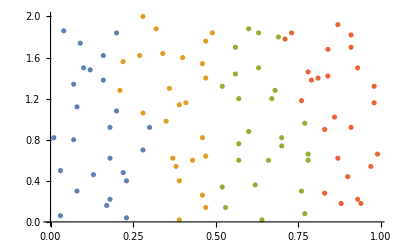

```mathematica
ListPlot[Partition[sample[[1]],25]]
```

```mathematica
(*************************métodos de clasificación: toca probar con varios para ver si alguno da resultados similares a la clasificación a mano. Sin embargo, el KMeans para ser un buen enfoque *)
```

```mathematica
SeedRandom[2]
Dis=MixtureDistribution[{2,2},{UniformDistribution[{{-0,1}, {0,1.5}}],
UniformDistribution[{{0,3},{ 2,2.2}}]}];
data=RandomVariate[Dis,2000];
ListPlot[data, PlotRange->All]
```

```mathematica
ListPlot[FindClusters[data, 2, Method->"KMeans"]]
```

-Graphics-

### Uploading data1

```mathematica
(**With the first sample : RandomChoice***************)
```

```mathematica
sample=Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/kgγgSamples.csv"]//ToExpression;
```

```mathematica
sample//Dimensions
```

{10,100,2}

```mathematica
data=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/outDataStatisticalA/controlUnRGA_sample"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3}}]//Association;
```

```mathematica
data//Dimensions
```

{298}

```mathematica
data[[1]]//Dimensions
```

{100,2,8}

```mathematica
MapAt[{Mean[#],StandardDeviation[#]}&,MapAt[Transpose,MapAt[Flatten,Transpose/@data,{All,All,All}],{All,All}],{All,All,All}];
```

```mathematica
%[[1]]//Dimensions
```

{2,26}

```mathematica
meanSDparaSets=%;
```

```mathematica
meanSDparaSets//Dimensions
```

{298}

```mathematica
meanSDparaSets[[1]]//Dimensions
```

{2,26,2}

```mathematica
Export["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/meanSDparaSets.csv",meanSDparaSets];
```

```mathematica
meanSDparaSetsmRNAmean=meanSDparaSets[[All,1,All,1]];
meanSDparaSetsmRNAsd=meanSDparaSets[[All,1,All,2]];
meanSDparaSetsProteinMean=meanSDparaSets[[All,2,All,1]];
meanSDparaSetsProteinMean=meanSDparaSets[[All,2,All,2]];
```

```mathematica
meanSDparaSetsmRNAmean[[1]]//Dimensions
```

{26}

```mathematica
meanSDparaSetsmRNAmean[[1;;2]]//N
```

<|{0.03,0.06}→{3.50448,0.47314,0.229835,15.5741,7.28821,55.2392,15.5741,306.079,6984.77,177408.,4.89058×10^6,1.43959×10^8,4.47458×10^9,1.45676×10^11,4.93725×10^12,1.73354×10^14,0.,55.2375,114.878,8313.66,50508.7,2.03986×10^6,2.23896×10^7,7.01074×10^8,1.09927×10^10,3.07019×10^11},{0.08,0.3}→{1.75978,0.439512,0.196944,9.04208,3.94938,16.2247,9.04208,100.563,1308.22,19327.7,317507.,5.70115×10^6,1.1026×10^8,2.26771×10^9,4.9067×10^10,1.10704×10^12,0.,16.224,33.2767,876.909,5311.5,91886.5,934146.,1.4676×10^7,1.92149×10^8,3.02284×10^9}|>

```mathematica
data[[1,1,1]]//N(*Estimados para una replica de mRNA *)
```

{2.7271,0.539355,0.290904,9.37457,5.05622,25.5654,{9.37457,113.447,1581.56,24231.8,399198.,6.9907×10^6,1.2921×10^8,2.50672×10^9,5.07758×10^10,1.068×10^12},{0.,25.5642,38.741,1575.87,8270.38,169442.,1.68241×10^6,2.74943×10^7,3.58781×10^8,5.52318×10^9}}

```mathematica
{"ff[i]", "cv[i]","cv2[i]", "Mean[i]","StandardDeviation[i]","Variance[i]","Table[Moment[i,j],{j,10}]","Table[CentralMoment[i,j],{j,10}]"}//PositionIndex
```

<|ff[i]→{1},cv[i]→{2},cv2[i]→{3},Mean[i]→{4},StandardDeviation[i]→{5},Variance[i]→{6},Table[Moment[i,j],{j,10}]→{7},Table[CentralMoment[i,j],{j,10}]→{8}|>

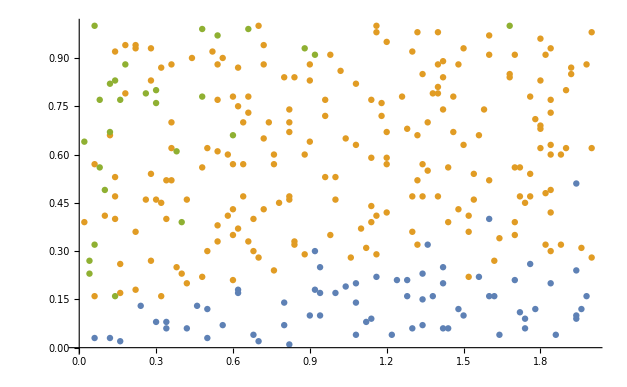

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4,Sequence@@Range[17,26]}]]],{All,All}]](*ff,cv2,mean,con solo los centralMoments***********BUENA*)
```

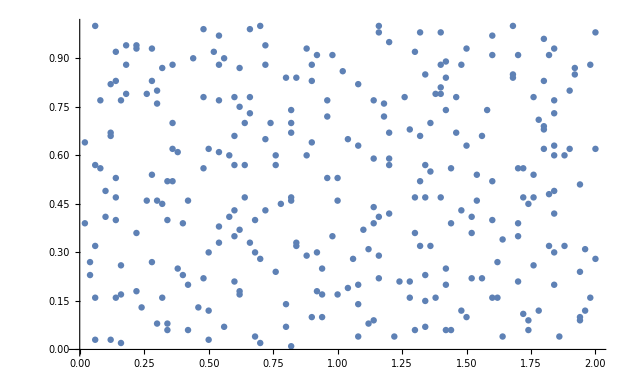

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,17;;26]]],{All,All}]](*con solo los centralMoments*)
```

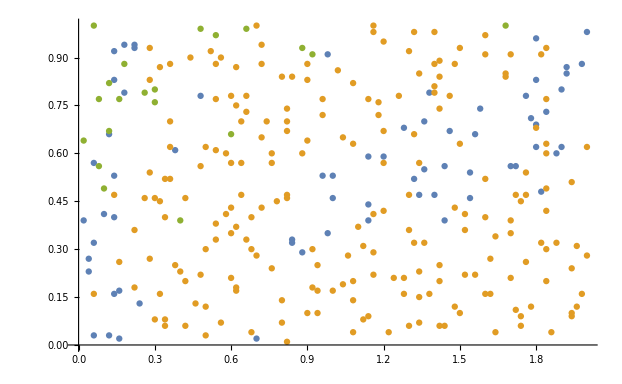

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4,Sequence@@Range[7,16]}]]],{All,All}]](*ff,cv2,mean,con solo los rawMoments*)
```

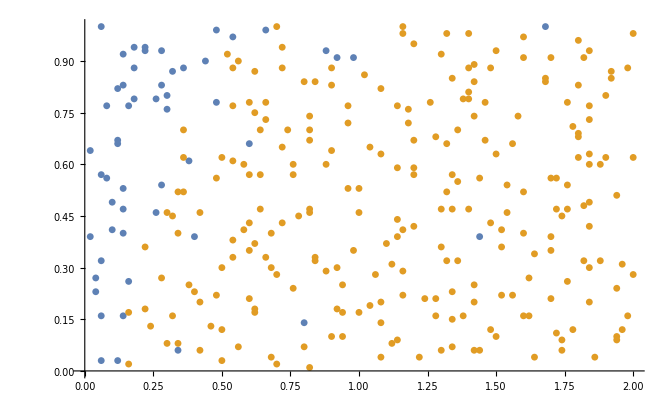

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,7;;16]]],{All,All}]](*con solo los rawMoments*)
```

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4,5}]]],{All,All}]]
```

$Aborted

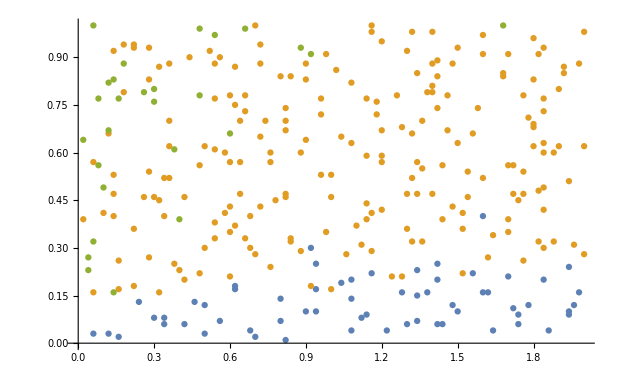

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4,6}]]],{All,All}]]
```

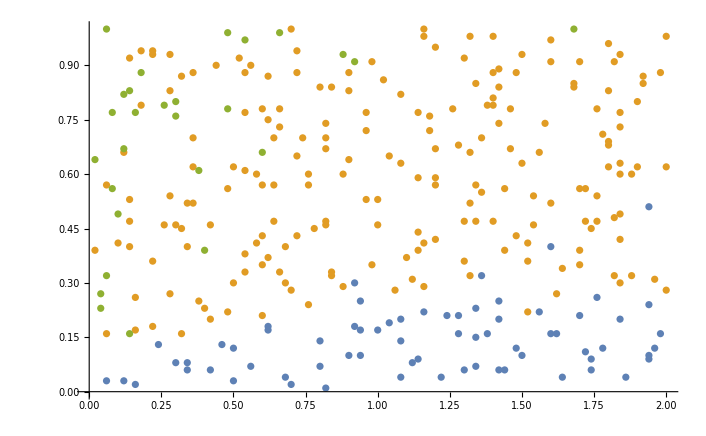

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4}]]],{All,All}]]
```

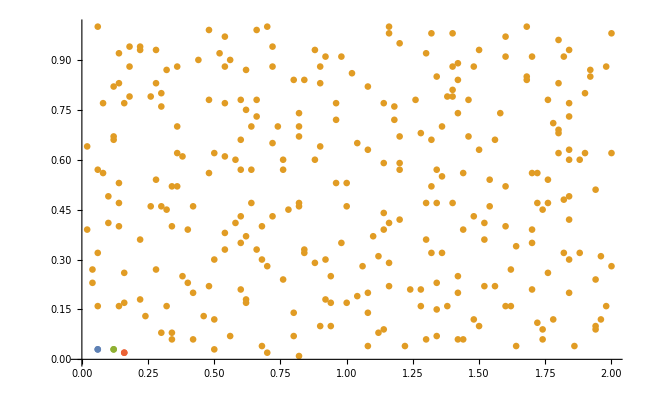

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4}]],4],{All,All}]]
```

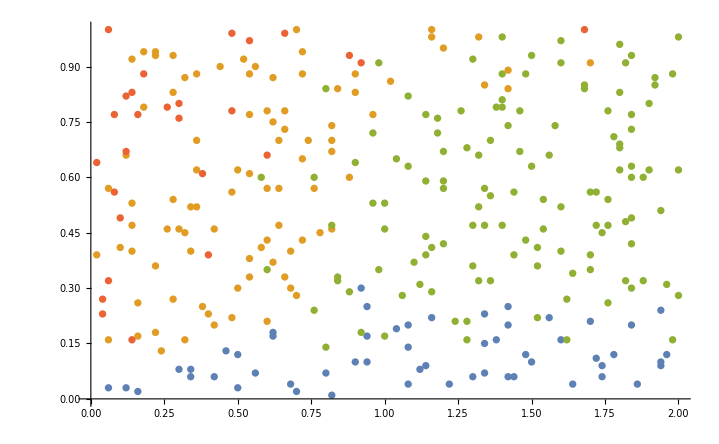

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4}]],4,Method->"KMeans"],{All,All}]]
```

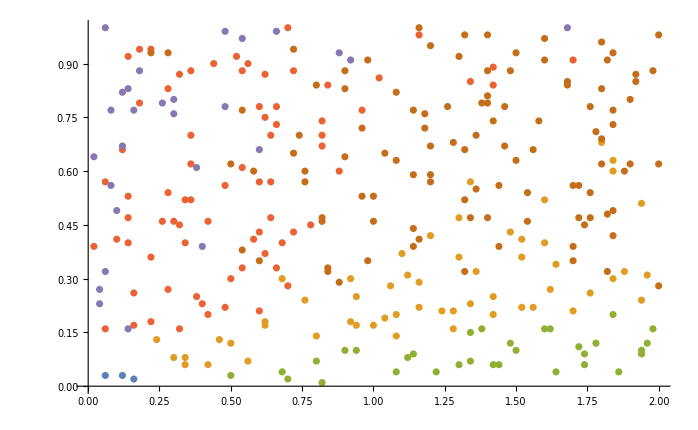

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4}]],6,Method->"KMeans"],{All,All}]]
```

### Uploading data2

```mathematica
(**With the first sample : RandomSample + Kurtosis + Skweness***************)
```

```mathematica
sample=Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/kgγgSamples.csv"]//ToExpression;
```

```mathematica
sample//Dimensions
```

{10,100,2}

```mathematica
data=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/outDataStatisticalA/controlUnRGA_sample_"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3,4,5}}]//Association;
```

```mathematica
data//Dimensions
```

{500}

```mathematica
(*****para verificar que no se tengan archivos faltantes*)
```

```mathematica
Table[data[[i]]//Dimensions,{i,1,Length[data]}]//DeleteDuplicates
```

{{100,2,10}}

```mathematica
data[[8]]
```

```mathematica
{{}}
```

```mathematica
data=DeleteCases[data,{}]/.{}->Nothing;
```

```mathematica
Table[data[[i]]//Dimensions,{i,1,Length[data]}]
```

{{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{}}

```mathematica
data=data[[1;;-10]];
```

```mathematica
data[[1,1]]//Dimensions
```

{2,10}

```mathematica
(********************************************)
```

```mathematica
MapAt[{Mean[#],StandardDeviation[#]}&,MapAt[Transpose,MapAt[Flatten,Transpose/@data,{All,All,All}],{All,All}],{All,All,All}];
```

```mathematica
%%%[[1]]//Dimensions
```

{2,28,2}

```mathematica
meanSDparaSets=%;
```

```mathematica
meanSDparaSets//Dimensions
```

{183}

```mathematica
meanSDparaSets[[1]]//Dimensions(* mRNA/protein - 18 estimators - mean/sd *)
```

{2,28,2}

```mathematica
Export["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/meanSDparaSets.csv",meanSDparaSets];
```

```mathematica
meanSDparaSets=Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/meanSDparaSets.csv"]//ToExpression;
```

$Aborted

```mathematica
meanSDparaSetsmRNAmean=meanSDparaSets[[All,1,All,1]];
meanSDparaSetsmRNAsd=meanSDparaSets[[All,1,All,2]];
meanSDparaSetsProteinMean=meanSDparaSets[[All,2,All,1]];
meanSDparaSetsProteinMean=meanSDparaSets[[All,2,All,2]];
```

```mathematica
meanSDparaSetsmRNAmean[[1]]//Dimensions
```

{28}

```mathematica
meanSDparaSetsmRNAmean[[1;;2]]//N
```

<|{0.08,0.3}→{1.86237,0.451115,0.206674,9.02662,4.06852,17.2355,2.69497,0.402293,9.02662,100.854,1321.82,19668.3,324456.,0.,17.2347,36.3618,948.257,5747.91},{0.03,0.5}→{1.36812,0.600035,0.36597,3.7478,2.24533,5.51088,2.79079,0.52807,3.7478,20.6211,145.898,1245.45,12234.2,0.,5.5101,8.75165,117.049,518.39}|>

```mathematica
data[[1,1,1]]//N(*Estimados para una replica de mRNA *)
```

{1.66928,0.438061,0.191897,8.69881,3.8106,14.5207,3.15546,0.446828,{8.69881,90.189,1061.87,13843.5,196473.},{0.,14.5198,24.7218,665.246,3450.07}}

```mathematica
{"ff[i]", "cv[i]","cv2[i]", "Mean[i]","StandardDeviation[i]","Variance[i]","Kurtosis[i]","Skewness[i]","Table[Moment[i,j],{j,10}]","Table[CentralMoment[i,j],{j,10}]"}//PositionIndex
```

<|ff[i]→{1},cv[i]→{2},cv2[i]→{3},Mean[i]→{4},StandardDeviation[i]→{5},Variance[i]→{6},Kurtosis[i]→{7},Skewness[i]→{8},Table[Moment[i,j],{j,10}]→{9},Table[CentralMoment[i,j],{j,10}]→{10}|>

#### mRNA

```mathematica
(************************************************************+)
```

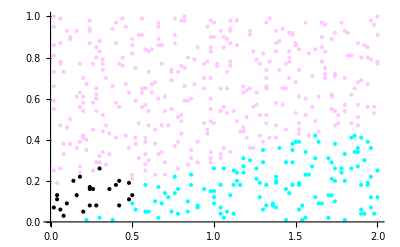

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{1,3,4}]]],{All,All}],PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean*)
```

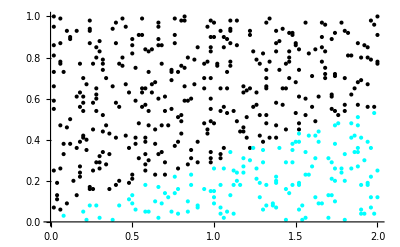

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{1,3,4,6}]]],{All,All}],PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean,var*)
```

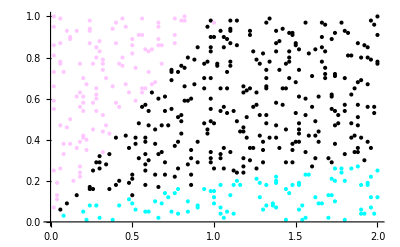

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{1,3,4}]],3,Method->"KMeans"],{All,All}],PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean*)
```

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{1,3,4}]],Method->"GaussianMixture"],{All,All}],PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean*)
```

-Graphics-

```mathematica
(******************************************************************************************+)
```

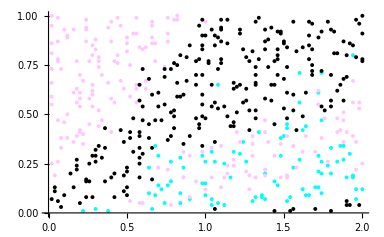

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{1,3,4,7}]]],{All,All}],PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean, kurtosis*)
```

```mathematica
(******************************************************************+Evaluationg the Skeweness*)
```

```mathematica
MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{1,3,4,8}]]],{All,All}];
```

$Aborted

```mathematica
MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,8]]//N],{All,All}];
```

$Aborted

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,8]],4,Method->"KMeans"],{All,All}]]
```

$Aborted

```mathematica
meanSDparaSetsmRNAmean[[All,8]][[1;;10]]//N
```

<|{0.06,0.06}→0.434638,{0.01,0.38}→0.416672,{0.05,0.6}→0.420325,{0.05,0.74}→0.37446,{0.07,0.9}→0.406353,{0.02,1.06}→0.406111,{0.07,1.38}→0.400682,{0.02,1.56}→0.388333,{0.1,1.74}→0.422539,{0.04,1.9}→0.415998|>

```mathematica
ListPlot[%,PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean,skewness*)
```

$Aborted

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{1,3,4,7,8}]]],{All,All}]](*ff,cv2,mean,curtosis,skewness*)
```

$Aborted

```mathematica
(*************************************************************+)
```

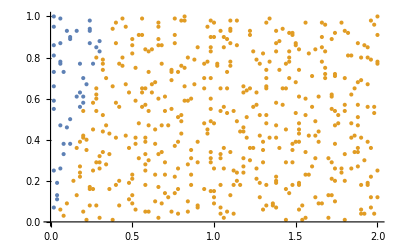

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{Sequence@@Range[9,19]}]]],{All,All}]](*con solo los rawMoments*)
```

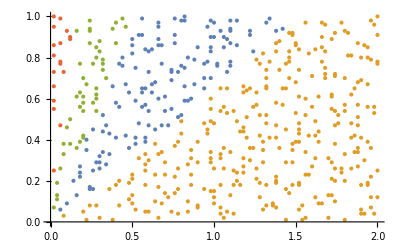

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{Sequence@@Range[9,19]}]],4,Method->"KMeans"],{All,All}]](*con solo los rawMoments*)
```

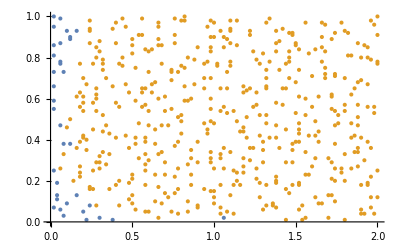

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{1,3,4,Sequence@@Range[9,19]}]]],{All,All}]](*con solo los rawMoments*)
```

```mathematica
(*******************************************************************)
```

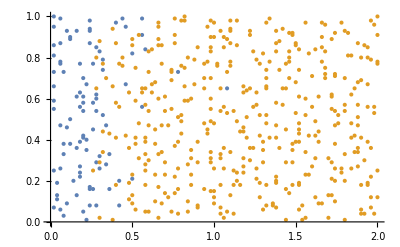

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{Sequence@@Range[19,28]}]]],{All,All}]](*con solo los centralMoments*)
```

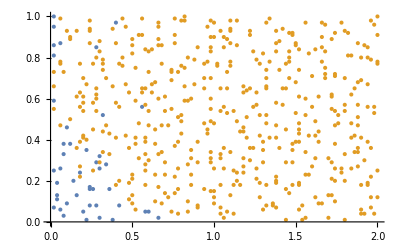

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsmRNAmean[[All,{1,3,4,Sequence@@Range[19,28]}]]],{All,All}]](*con solo los centralMoments*)
```

```mathematica
(********************************************************************)
```

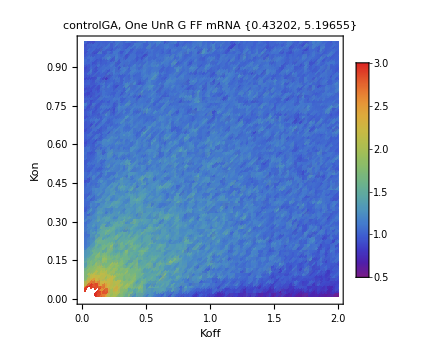
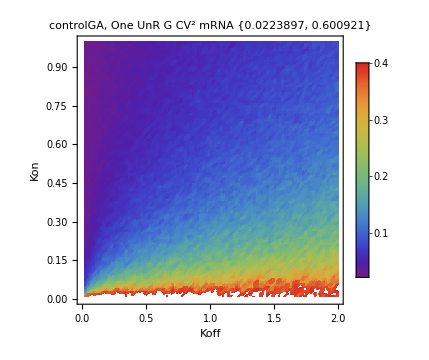
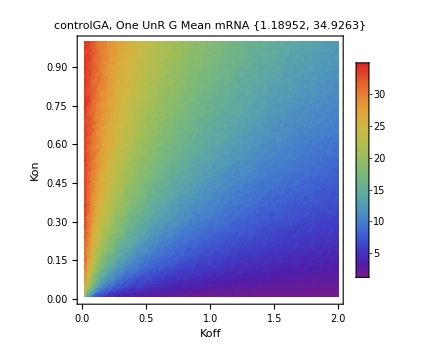
```mathematica
plotsUnR={-Graphics-,-Graphics-,-Graphics-};
```

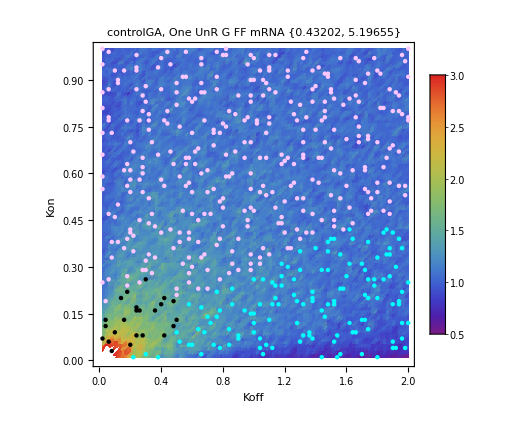
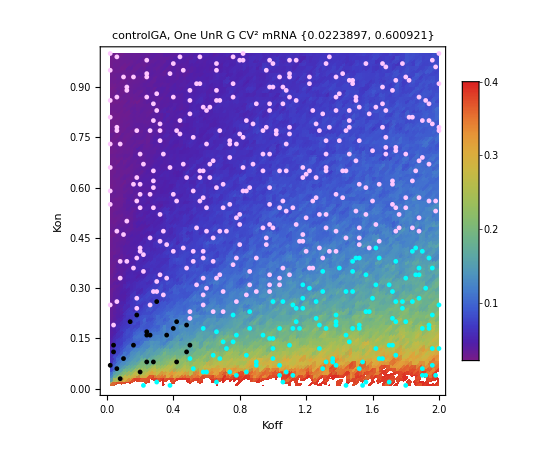
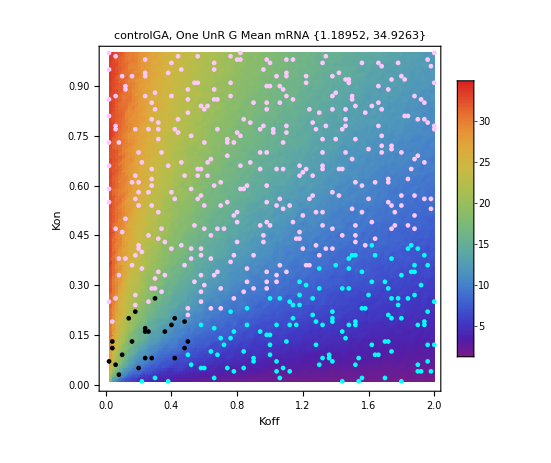

```mathematica
Show[plotsUnR[[#]],%124]&/@{1,2,3}
```

#### protein

```mathematica
(*************finding the default settings*)
```

```mathematica
AbsoluteOptions[FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4}]],Method->Automatic],Method]
```

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4}]],Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{}

```mathematica
Rule["Method",_]
```

Method→_

```mathematica
Flatten@Trace[FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4}]],Method->Automatic],HoldPattern[Rule[Method,_]],TraceInternal->True]
```

{Method→Automatic,Method→Automatic,Method→Automatic,Method→Automatic,Method→ParallelMersenneTwister,Method→ParallelMersenneTwister}

```mathematica
Trace[FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4}]],Method->Automatic]]
```

{1}
 |  |  |  |

```mathematica
(************************************************************+)
```

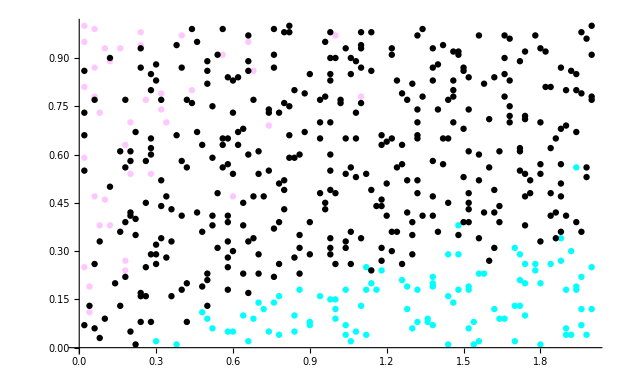

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4}]]],{All,All}],PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean*)
```

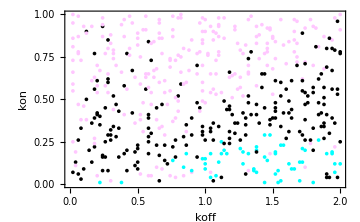

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4,6}]]],{All,All}],PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean,var*)
```

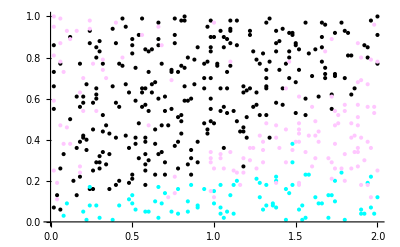

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4}]],3,Method->"KMeans"],{All,All}],PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean*)
```

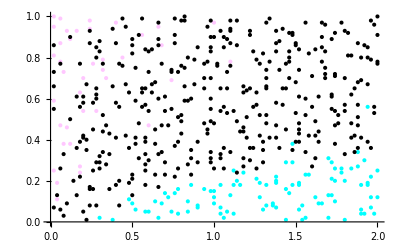

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4}]],Method->"GaussianMixture"],{All,All}],PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean*)
```

```mathematica
(******************************************************************************************+)
```

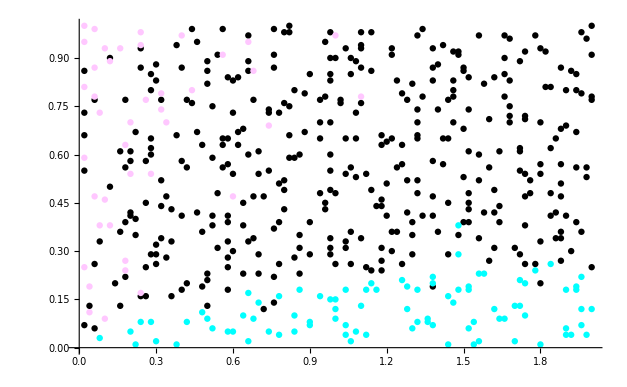

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4,7}]]],{All,All}],PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean, kurtosis*)
```

```mathematica
(******************************************************************+Evaluationg the Skeweness*)
```

```mathematica
MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4,8}]]],{All,All}];
```

$Aborted

```mathematica
MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,8]]//N],{All,All}];
```

$Aborted

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,8]],4,Method->"KMeans"],{All,All}]]
```

$Aborted

```mathematica
meanSDparaSetsProteinMean[[All,8]][[1;;10]]//N
```

<|{0.06,0.06}→0.434638,{0.01,0.38}→0.416672,{0.05,0.6}→0.420325,{0.05,0.74}→0.37446,{0.07,0.9}→0.406353,{0.02,1.06}→0.406111,{0.07,1.38}→0.400682,{0.02,1.56}→0.388333,{0.1,1.74}→0.422539,{0.04,1.9}→0.415998|>

```mathematica
ListPlot[%,PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean,skewness*)
```

$Aborted

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4,7,8}]]],{All,All}]](*ff,cv2,mean,curtosis,skewness*)
```

$Aborted

```mathematica
(*************************************************************+)
```

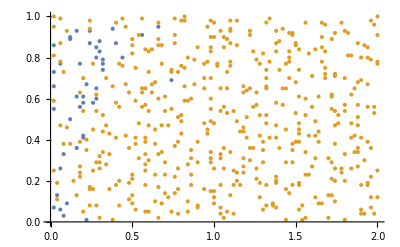

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{Sequence@@Range[9,19]}]]],{All,All}]](*con solo los rawMoments*)
```

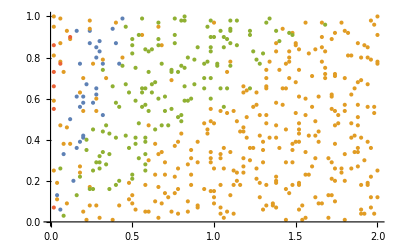

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{Sequence@@Range[9,19]}]],4,Method->"KMeans"],{All,All}]](*con solo los rawMoments*)
```

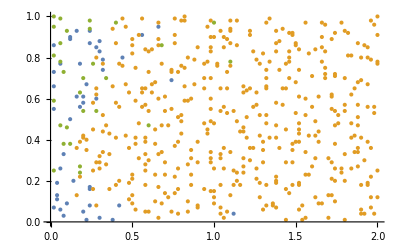

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4,Sequence@@Range[9,19]}]]],{All,All}]](*con solo los rawMoments*)
```

```mathematica
(*******************************************************************)
```

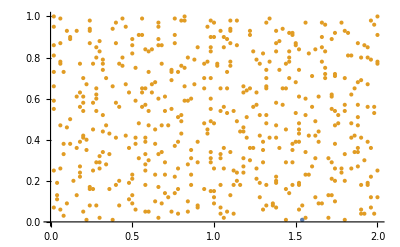

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{Sequence@@Range[19,28]}]]],{All,All}]](*con solo los centralMoments*)
```

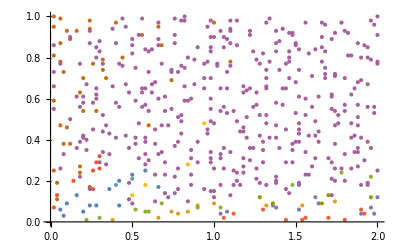

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean[[All,{1,3,4,Sequence@@Range[19,28]}]]],{All,All}]](*con solo los centralMoments*)
```

```mathematica
(********************************************************************)
```

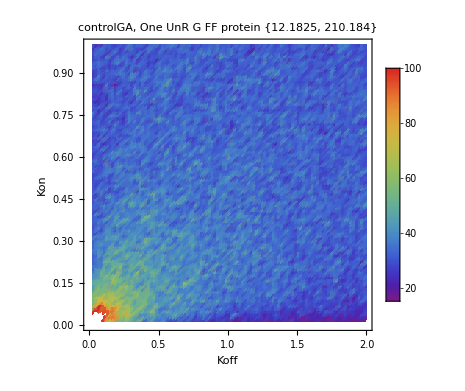
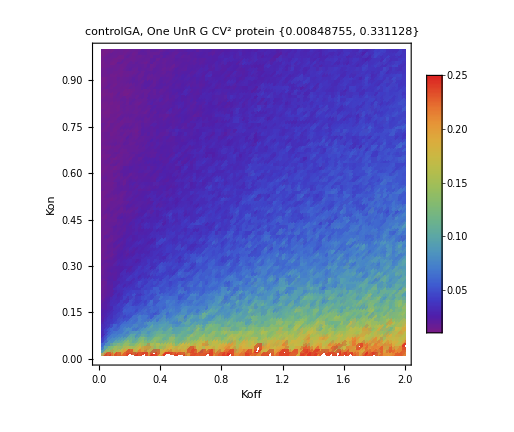
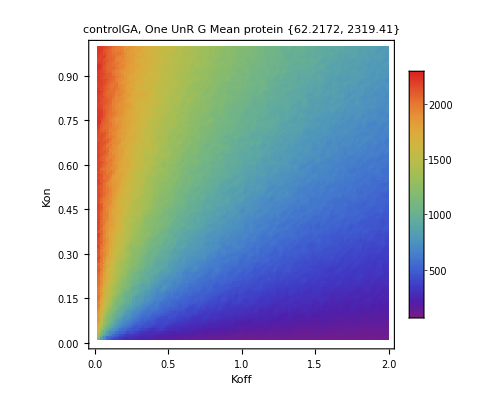
```mathematica
plotsUnR2={-Graphics-,-Graphics-,-Graphics-};
```

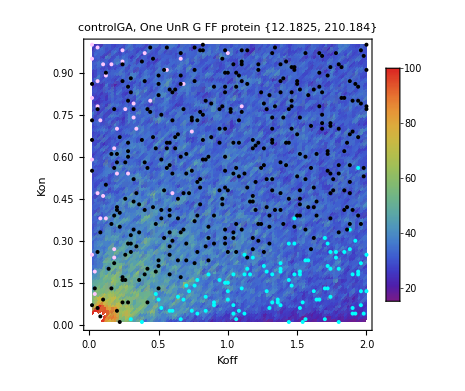
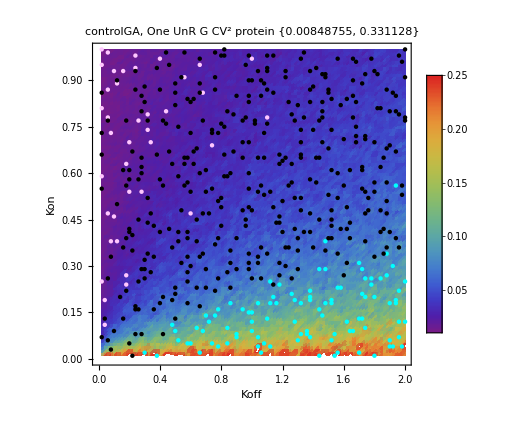
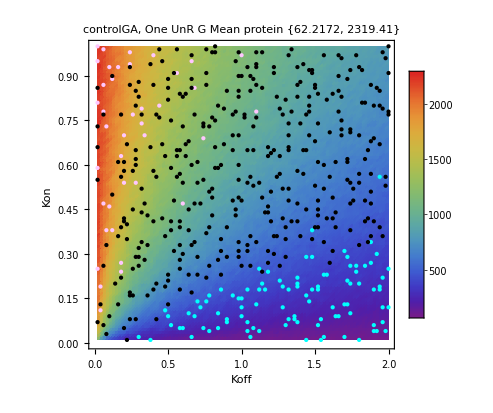

```mathematica
Show[plotsUnR2[[#]],%138]&/@{1,2,3}
```

## Plotting the estimates

Here we made plots by estimated. So for example, it is possible to identify the regions with more skewness

```mathematica
sample=Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/kgγgSamples.csv"]//ToExpression;
```

```mathematica
data=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/outDataStatisticalA/controlUnRGA_sample_"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3,4,5}}]//Association;
```

```mathematica
MapAt[{Mean[#],StandardDeviation[#]}&,MapAt[Transpose,MapAt[Flatten,Transpose/@data,{All,All,All}],{All,All}],{All,All,All}];
```

```mathematica
meanSDparaSetsmRNAmean=meanSDparaSets[[All,1,All,1]];
meanSDparaSetsmRNAsd=meanSDparaSets[[All,1,All,2]];
meanSDparaSetsProteinMean=meanSDparaSets[[All,2,All,1]];
meanSDparaSetsProteinMean=meanSDparaSets[[All,2,All,2]];
```

```mathematica
{"ff[i]", "cv[i]","cv2[i]", "Mean[i]","StandardDeviation[i]","Variance[i]","Kurtosis[i]","Skewness[i]","Table[Moment[i,j],{j,10}]","Table[CentralMoment[i,j],{j,10}]"}//PositionIndex
```

<|ff[i]→{1},cv[i]→{2},cv2[i]→{3},Mean[i]→{4},StandardDeviation[i]→{5},Variance[i]→{6},Kurtosis[i]→{7},Skewness[i]→{8},Table[Moment[i,j],{j,10}]→{9},Table[CentralMoment[i,j],{j,10}]→{10}|>

```mathematica
Apply[ListPlot3D[Map[{Sequence@@Reverse[#[[1]]],#[[2]]//N}&,meanSDparaSetsProteinMean[[All,#1]]//Normal],ImageSize->Medium,AxesLabel->{"koff","kon",#2}]&]/@{{1,"FF"},{2,"CV"},{3,"CV2"},{4,"Mean"},{5,"SD"},{6,"Var"},{7,"Kurtossis"},{8,"Ske"}}
```

General::munfl: 1/220416287179745948740640966753346733376420412751195822790162742372415000297642028279474652504608604926189739141840821538097955092718532985350708356136671857415293641957280350787342665010241042439268715174178150200916863561525284680816176046629207793372900864306503276555027412996328060332852309440485445944808636246040000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/19199652849838272917228242844401732058516564661554472215218158734980890098657950941513162518346984497206611571963071043134657550223381075871964971195235289610401570994906693915268568321945753500555608337189922955238021263015957066098380418542922762158879394368271279553739488795087558816613195070380249157593038046263742064840730000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/4858343594492932805039463624181711463232418874239077940992661908800106435995134786302583353695564889094038925204016779309797744609613373397323640048487894501190798543471485685222730708580015552416830303721577462709634068265101879337193072554937407205412417054669824548955354957227294169064675079736317565032476718471948067144900503328257922329600 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(*CONCLUTIONS FOR THE CHARACTERISTICS OF THE STEADY-STATE TEMPORAL DYNAMIC or STATES DISTRIBUTION :
 1. CV2 is smother then CV
2. Mean a SD have similar pattern
3. FF and Var have similar pattern
4. All the distribution of expression are mesocurtic
5. There is not pattern in the Skewness *)
```

```mathematica
Power[{2,3},2]
```

{4,9}

```mathematica
(meanSDparaSetsProteinMean[[All,6]]//Values)[[1]]//N
```

General::munfl: 1/(2883687988976148745860904579932120988223621525427334602663976904074200818438877938416223611194572641174010527447587698958358576638396262322350960427585837024188893828804849008427169467430443667947645930299110808557261247349527«156»2857737156982946852950279773855575730741721774466602535166547205191840612402930411514462489818728421903732647543750635808368524779212142435409430423656505446690647214557137390923740696161845540731326860231412948911164932808000) is too small to represent as a normalized machine number; precision may be lost.

0.

General::munfl: 1/(2883687988976148745860904579932120988223621525427334602663976904074200818438877938416223611194572641174010527447587698958358576638396262322350960427585837024188893828804849008427169467430443667947645930299110808557261247349527«156»2857737156982946852950279773855575730741721774466602535166547205191840612402930411514462489818728421903732647543750635808368524779212142435409430423656505446690647214557137390923740696161845540731326860231412948911164932808000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/642657803007004724126243283062597959466319719651143467576100932354467789492828816415017300668169076114185377670116111131146089116624826556627179272986671651889909827645689598109476695332870509197392622012725707241836804156240219294823388476296957896745325054232335379978065559369232884086190064134161950988618530310715698412977064383059725906082032044298018223809508615770491595259576816592084573280000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/3192768621869009667963267009302697084557293088976950476690058008075989451956935570094188950579079551332216683839245828686705626643431587882831424179140583161137804587762952872998926929570811342486544014417883487162669490835193742682101260895241539829738950271776510560410864434064635859940107246737114424233810118080519522873543477227183302769135840990137628960025707487492457499125189306650306560000 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

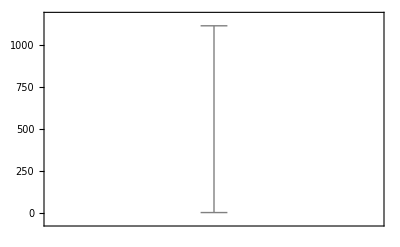

```mathematica
BoxWhiskerChart[meanSDparaSetsProteinMean[[All,6]]//Values]
```

```mathematica
BoxWhiskerChart[Power[meanSDparaSetsProteinMean[[All,5]]//Values,2]]
```

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ….

$Aborted

## Comparison

```mathematica
sample=Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/kgγgSamples.csv"]//ToExpression;
```

```mathematica
data2=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/outDataStatisticalA/controlRGA_sample_"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3,4,5}}]//Association;
```

```mathematica
data2//Dimensions
```

{500}

```mathematica
Table[data2[[i]]//Dimensions,{i,1,Length[data2]}]//DeleteDuplicates
```

{{100,2,10}}

```mathematica
MapAt[{Mean[#],StandardDeviation[#]}&,MapAt[Transpose,MapAt[Flatten,Transpose/@data2,{All,All,All}],{All,All}],{All,All,All}];
```

```mathematica
meanSDparaSets2=%;
```

```mathematica
meanSDparaSets[[1]]//Dimensions(* mRNA/protein - 18 estimators - mean/sd *)
```

{2,28,2}

```mathematica
meanSDparaSetsmRNAmean2=meanSDparaSets2[[All,1,All,1]];
meanSDparaSetsmRNAsd2=meanSDparaSets2[[All,1,All,2]];
meanSDparaSetsProteinMean2=meanSDparaSets2[[All,2,All,1]];
meanSDparaSetsProteinMean2=meanSDparaSets2[[All,2,All,2]];
```

```mathematica
{"ff[i]", "cv[i]","cv2[i]", "Mean[i]","StandardDeviation[i]","Variance[i]","Kurtosis[i]","Skewness[i]","Table[Moment[i,j],{j,10}]","Table[CentralMoment[i,j],{j,10}]"}//PositionIndex
```

<|ff[i]→{1},cv[i]→{2},cv2[i]→{3},Mean[i]→{4},StandardDeviation[i]→{5},Variance[i]→{6},Kurtosis[i]→{7},Skewness[i]→{8},Table[Moment[i,j],{j,10}]→{9},Table[CentralMoment[i,j],{j,10}]→{10}|>

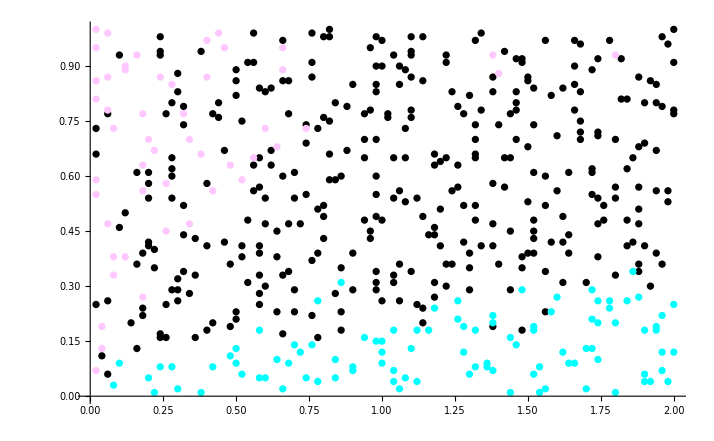

```mathematica
ListPlot[MapAt[Reverse,FindClusters[meanSDparaSetsProteinMean2[[All,{1,3,4}]]],{All,All}],PlotStyle->{Black,Cyan,RGBColor[1, 0.78, 1]}](*ff,cv2,mean*)
```

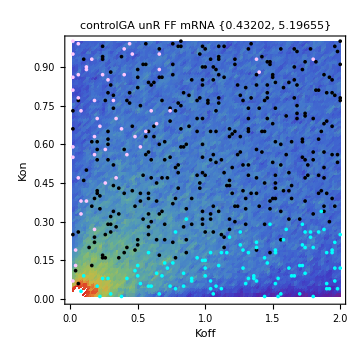
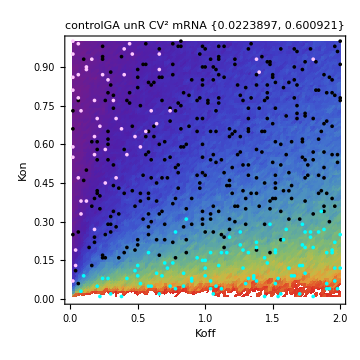
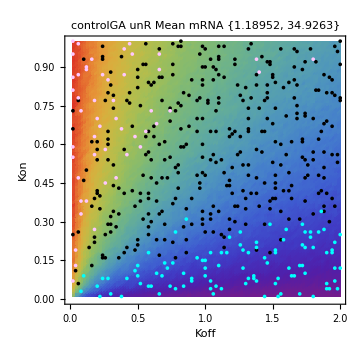

```mathematica
Show[plot[[#]],%14]&/@{1,2,3}(**Here it is overlap the groups of oneR gene *)
```

```mathematica
(**Here it is overlap the groups of oneUnR gene *)
```

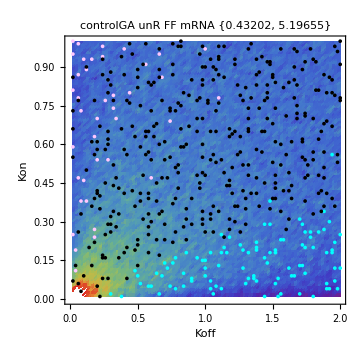
```mathematica
-Graphics-,-Graphics-,-Graphics-}
```